```mathematica
Swap[state_,tu_]:=
Module[{},a = state;
a[[tu]] = a[[Reverse[tu]]];
a];
noOverlap[pairs_]:=AllTrue[Permutations[pairs,{2}],{}===Intersection@@#&]
```

{0,0,0,0,0,1,1,1,1}

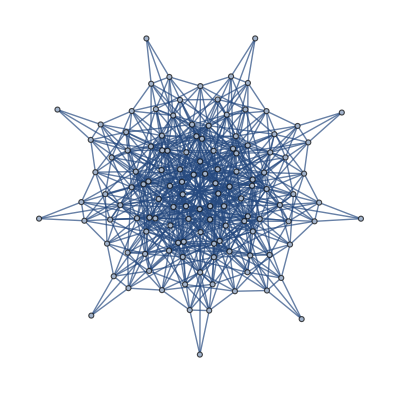

Set::wrsym: Symbol ⅇ is Protected.

```mathematica
(*A nice way to use only two variables for generating states*)
n = 9;
energy = 4;
edges = {};
s = {};
For[i=0,i<(n-energy ),i++, AppendTo[s,0]]
For[j = 0,j<energy ,j++,AppendTo[s,1]]
Print[s]
allStates = Permutations[s];
swaps = Partition[Append[Range[n],1],2,1];

edges = 
Union[
Flatten[
Table[
Flatten[
Table[
If[noOverlap[{p1,p2}],
state<-> Swap[Swap[state,p1],p2],
Nothing],

{p1,swaps},{p2,swaps}
]
]
,
{state, allStates}]
]
];

SimpleGraph[edges]
```

```mathematica
(*A nice way to use only two variables for generating states*)
n = 9;
For[energy=0,energy<n,energy++,
edges = {};
s = {};
For[i=0,i<(n-energy ),i++, AppendTo[s,0]]
For[j = 0,j<energy ,j++,AppendTo[s,1]]
Print[s]
allStates = Permutations[s];
swaps = Partition[Append[Range[n],1],2,1];
edges = 
Union[
Flatten[
Table[
Flatten[
Table[
If[noOverlap[{p1,p2}],
state<-> Swap[Swap[state,p1],p2],
Nothing],

{p1,swaps},{p2,swaps}
]
]
,
{state, allStates}]
]
];

SimpleGraph[edges]
]
```

{0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,1}

{0,0,0,0,0,0,0,1,1}

{0,0,0,0,0,0,1,1,1}

{0,0,0,0,0,1,1,1,1}

{0,0,0,0,1,1,1,1,1}

{0,0,0,1,1,1,1,1,1}

{0,0,1,1,1,1,1,1,1}

{0,1,1,1,1,1,1,1,1}